C:\Users\liupe\Desktop\biduffing\Code\bistable_para_duffing_x2

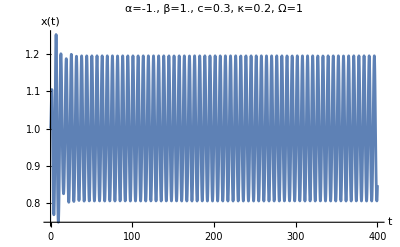

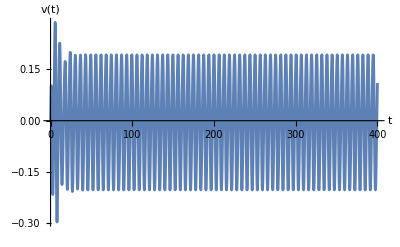

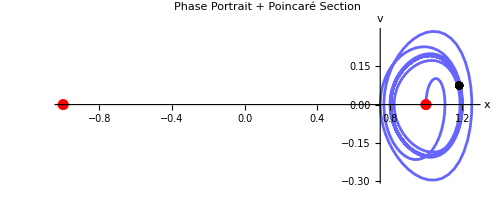

```mathematica
SetDirectory@NotebookDirectory[]
ClearAll[FindStableEq,IntegrateAndPlotForced];

(*仅用于给初值定位左右井的"参考静平衡"（只看 F0，不含 Cos 项）*)
FindStableEq[α_,β_,F0_]:=Module[{xs},xs=x/. NSolve[β x^3+α x-F0==0,x,Reals];
Sort@Select[xs,(α+3 β #^2)>0&]];

(*修改后的函数：方程 ẍ+cẋ+αx+βx.b3=κ cos(Ωt) x.b2*)
IntegrateAndPlotForced[α_:-1.,β_:1.,c_:0.3,κ_:0.2,Ω_:1,tmax_:400.,dt_:0.001,ic_:Automatic,tSettle_:20.]:=Module[{stables,x0,v0,xFun,vFun,t,T,tgrid,xPlot,vPlot,phasePlot,eqPts,eqOverlay,poincT0,nP,poincPts,poincPlot},(*参考平衡点（无激励时，κ=0）*)stables=FindStableEq[α,β,0];
If[Length[stables]<2,Print["未找到两个稳定平衡（参考 F0=0）。请检查 α<0, β>0。"];
Return[$Failed]];
{x0,v0}=If[ic===Automatic,{stables[[2]],0.0},ic];
T=2 Pi/Ω;(*激励周期*)Clear[x,v,t];
(*运动方程：ẍ+cẋ+αx+βx.b3=κ cos(Ωt) x.b2*){xFun,vFun}=NDSolveValue[{x'[t]==v[t],v'[t]==-c v[t]-α x[t]-β x[t]^3+κ Cos[Ω t] x[t]^2,x[0]==x0,v[0]==v0},{x,v},{t,0,tmax},Method->"ExplicitRungeKutta"];
tgrid=N@Range[0,tmax,dt];
(*时间历程图*)xPlot=Plot[xFun[t],{t,0,tmax},AxesLabel->{"t","x(t)"},PlotRange->All,PlotLabel->StringForm["α=``, β=``, c=``, κ=``, Ω=``",α,β,c,κ,Ω]];
vPlot=Plot[vFun[t],{t,0,tmax},AxesLabel->{"t","v(t)"},PlotRange->All];
(*相图*)phasePlot=ParametricPlot[{xFun[t],vFun[t]},{t,0,tmax},AxesLabel->{"x","v"},PlotRange->All,PlotStyle->Directive[Opacity[0.6],Blue]];
(*参考平衡点标记*)eqPts=Thread[{stables,0}];
eqOverlay=Graphics[{Red,PointSize[0.02],Point[eqPts]}];
(*Poincaré 截面采样（去掉过渡段）*)poincT0=Max[tSettle,5 T];
nP=Floor[(tmax-poincT0)/T];
poincPts=Table[{xFun[poincT0+k T],vFun[poincT0+k T]},{k,0,nP}];
poincPlot=ListPlot[poincPts,PlotStyle->Black,PlotMarkers->{Automatic,8}];
Print@xPlot;
Print@vPlot;
Show[phasePlot,eqOverlay,poincPlot,PlotLabel->"Phase Portrait + Poincaré Section"]];

(*默认调用*)
IntegrateAndPlotForced[]
```

数据生成配置：

方程: x'' + c*x' + α*x + β*x.b3 = κ*x.b2*cos(Ω*t)

频率 Ω: 21 点 [0.080 ~ 0.239 Hz]

幅值 κ: 13 点 {0,0.1,0.2,0.25,0.26,0.27,0.28,0.29,0.3,1,2,3,5}

总组合: 273

初值: x₀ ∈ {-1.00, 1.00}

进度: 20/273

进度: 40/273

进度: 60/273

进度: 80/273

进度: 100/273

进度: 120/273

进度: 140/273

进度: 160/273

进度: 180/273

进度: 200/273

进度: 220/273

进度: 240/273

进度: 260/273

进度: 273/273

数据抽样完成：

训练集: 873655 样本

验证集: 218400 样本

测试集: 218400 样本

统计信息：

输入 [x, v, κ*cos(Ωt), κ*sin(Ωt)]: μ = {0.00,0.00,0.00,0.00}, σ = {1.57,1.85,1.23,1.23}

输出 [ga]: μ = -0.001, σ = 5.290

✅ 数据已保存

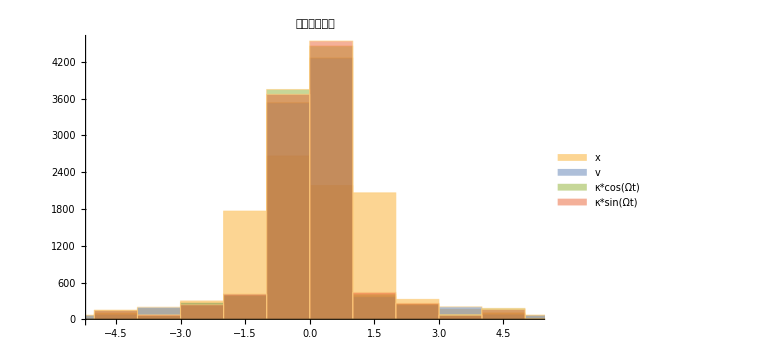

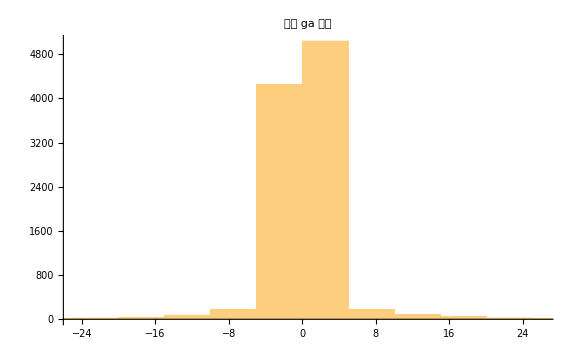

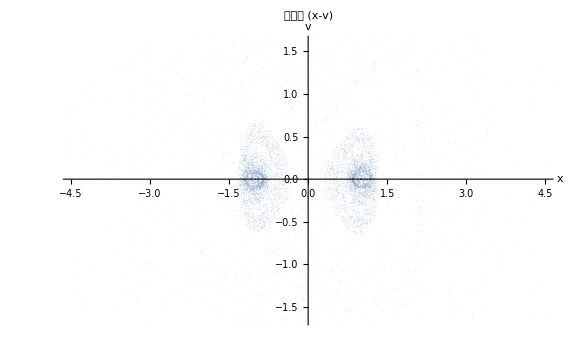

✅ 完成

```mathematica
(* ==================Duffing 二次参数激励振动：多激励幅值+分层采样==================*)(*方程：x''+c*x'+α*x+β*x.b3=κ*x.b2*Cos[Ω*t]*)(*目标：神经网络学习 ga=-c*v-α*x-β*x.b3+κ*x.b2*cos(Ω*t)*)ClearAll[α,β,c,FindStableEq,GenerateDataFromInitial,freqList,kappaList,allTrainData,allValData,allTestData,trainData,valData,testData,allInputs,allTargets,inputMean,inputStd,targetMeanGa,targetStdGa];

(*----------物理参数（双稳）----------*)
α=-1.;
β=1.;
c=0.3;

(*----------计算两个稳定静平衡----------*)
FindStableEq[α_,β_]:=Module[{xs},xs=x/. NSolve[β*x^3+α*x==0,x,Reals];
Sort@Select[xs,(α+3*β*#^2)>0&]];

stables=FindStableEq[α,β];
If[Length[stables]<2,Print["❌ 未找到两个稳定平衡，请检查参数。"];
Abort[];];

orix1=stables[[1]];
orix2=stables[[2]];

(*----------从一个初值生成数据----------*)
GenerateDataFromInitial[freq_,kappa_,orix_]:=Module[{Ω,tEnd,h,tgrid,xFun,vFun,xvals,vvals,kappaCos,kappaSin,data,list},Ω=freq*2*π;
tEnd=100./freq;
h=1./(200.*freq);
tgrid=N@Range[0,tEnd,h];
Clear[x,v,t];
(*修改后的方程：ẍ+cẋ+αx+βx.b3=κ x.b2 cos(Ωt)*){xFun,vFun}=NDSolveValue[{x'[t]==v[t],v'[t]==-c*v[t]-α*x[t]-β*x[t]^3+kappa*x[t]^2*Cos[Ω*t],x[0]==orix,v[0]==0.},{x,v},{t,0,tEnd},MaxStepSize->h/2];
xvals=xFun/@tgrid;
vvals=vFun/@tgrid;
kappaCos=kappa*Cos[Ω*tgrid];
kappaSin=kappa*Sin[Ω*tgrid];
data=Transpose[{xvals,vvals,kappaCos,kappaSin}];
(*修改目标函数：ga=-c*v-α*x-β*x.b3+κ*x.b2*cos(Ω*t)*)list=Table[With[{xvks=data[[i]],xval=xvals[[i]],vval=vvals[[i]],kc=kappaCos[[i]]},Module[{ga},ga=(-c*vval-α*xval-β*xval^3+kc*xval^2);
xvks->{ga}]],{i,Length[tgrid]}];
list];

(* ==================分层采样配置==================*)
freqList=Range[0.5,1.5,0.05]/2/π;  (*参数激励频率范围*)
kappaList={0,0.1,0.2,0.25,0.26,0.27,0.28,0.29,0.3,1,2,3,5};  (*参数激励幅值*)

Print["数据生成配置："];
Print["  方程: x'' + c*x' + α*x + β*x.b3 = κ*x.b2*cos(Ω*t)"];
Print["  频率 Ω: ",Length[freqList]," 点 [",NumberForm[freqList[[1]],{4,3}]," ~ ",NumberForm[freqList[[-1]],{4,3}]," Hz]"];
Print["  幅值 κ: ",Length[kappaList]," 点 ",kappaList];
Print["  总组合: ",Length[freqList]*Length[kappaList]];
Print["  初值: x₀ ∈ {",NumberForm[orix1,{4,2}],", ",NumberForm[orix2,{4,2}],"}"];

allTrainData={};
allValData={};
allTestData={};
totalCombinations=Length[freqList]*Length[kappaList];
currentCombination=0;

Do[Do[Module[{samples1,samples2,allSamplesCombo,shuffled,splitIdx},currentCombination++;
If[Mod[currentCombination,20]==0||currentCombination==totalCombinations,Print["  进度: ",currentCombination,"/",totalCombinations];];
samples1=GenerateDataFromInitial[freq,kappa,orix1];
samples2=GenerateDataFromInitial[freq,kappa,orix2];
allSamplesCombo=Join[samples1,samples2];
shuffled=RandomSample[allSamplesCombo];
splitIdx=Round[0.8*Length[shuffled]];
allTrainData=Join[allTrainData,shuffled[[1;;splitIdx]]];
allValData=Join[allValData,shuffled[[splitIdx+1;;-1]]];],{kappa,kappaList}],{freq,freqList}];

allTrainData=RandomSample[allTrainData];
allValData=RandomSample[allValData];

(* ==================随机抽取 10%==================*)
samplingRatio=0.1;
trainSize=Round[Length[allTrainData]*samplingRatio];
valSize=Round[Length[allValData]*samplingRatio];
testSize=Round[Length[allValData]*samplingRatio];

trainData=RandomSample[allTrainData,trainSize];
valData=RandomSample[allValData,valSize];
testData=RandomSample[allValData,testSize];

Print["数据抽样完成："];
Print["  训练集: ",Length[trainData]," 样本"];
Print["  验证集: ",Length[valData]," 样本"];
Print["  测试集: ",Length[testData]," 样本"];

(* ==================数据统计==================*)
allInputs=trainData[[All,1]];
allTargets=trainData[[All,2]];

inputMean=Mean[allInputs];
inputStd=StandardDeviation[allInputs];
targetMeanGa=Mean[allTargets[[All,1]]];
targetStdGa=StandardDeviation[allTargets[[All,1]]];

Print["统计信息："];
Print["  输入 [x, v, κ*cos(Ωt), κ*sin(Ωt)]: μ = ",NumberForm[inputMean,{4,2}],", σ = ",NumberForm[inputStd,{4,2}]];
Print["  输出 [ga]: μ = ",NumberForm[targetMeanGa,{6,3}],", σ = ",NumberForm[targetStdGa,{6,3}]];

(* ==================保存数据==================*)
Export[FileNameJoin[{Directory[],"trainData_quadratic_parametric.mx"}],trainData,"MX"];
Export[FileNameJoin[{Directory[],"valData_quadratic_parametric.mx"}],valData,"MX"];
Export[FileNameJoin[{Directory[],"testData_quadratic_parametric.mx"}],testData,"MX"];

normParams=<|"inputMean"->inputMean,"inputStd"->inputStd,"targetMeanGa"->targetMeanGa,"targetStdGa"->targetStdGa,"freqList"->freqList,"kappaList"->kappaList,"alpha"->α,"beta"->β,"damping"->c|>;

Export[FileNameJoin[{Directory[],"normParams_quadratic_parametric.mx"}],normParams,"MX"];

Print["✅ 数据已保存"];

(* ==================可视化==================*)
sampleSize=Min[10000,Length[trainData]];
sampledData=RandomSample[trainData,sampleSize];
sampledInputs=sampledData[[All,1]];
sampledTargets=sampledData[[All,2,1]];

fig1=Histogram[Transpose[sampledInputs],30,PlotLabel->"输入特征分布",ChartLegends->{"x","v","κ*cos(Ωt)","κ*sin(Ωt)"},ImageSize->Large];

fig2=Histogram[sampledTargets,50,PlotLabel->"输出 ga 分布",ImageSize->Large];

fig3=ListPlot[sampledInputs[[All,{1,2}]],PlotStyle->{PointSize[0.001],Opacity[0.3]},AxesLabel->{"x","v"},PlotLabel->"相空间 (x-v)",ImageSize->Large];

Print@fig1;
Print@fig2;
Print@fig3;

sampledInputsForExcel=sampledInputs[[All,{1,2}]];

Export[FileNameJoin[{Directory[],"phase_space_x_v.xlsx"}],sampledInputsForExcel,"XLSX"];

Print["✅ 完成"];
```

数据加载完成：

训练集: 873655 样本

验证集: 218400 样本

测试集: 218400 样本

总计: 1310455 样本

输入维度: 4, 输出维度: 1

开始多阶段训练...

========== Stage 1 : rounds=200, lr=0.0005 ==========

验证集评估：

RMSE = {0.0292}

Rel% = {0.55}

Score = 0.0292

✅ 更新最佳模型已保存

========== Stage 2 : rounds=3000, lr=0.0001 ==========

验证集评估：

RMSE = {0.0091}

Rel% = {0.17}

Score = 0.0091

✅ 更新最佳模型已保存

========== Stage 3 : rounds=200, lr=0.00005 ==========

验证集评估：

RMSE = {0.0086}

Rel% = {0.16}

Score = 0.0086

✅ 更新最佳模型已保存

========== Stage 4 : rounds=200, lr=0.00001 ==========

验证集评估：

RMSE = {0.0085}

Rel% = {0.16}

Score = 0.0085

✅ 更新最佳模型已保存

✅ 模型已保存

========================================

最终评估：

========================================

训练集评估：

RMSE = {0.0077}

Rel% = {0.15}

Score = 0.0077

验证集评估：

RMSE = {0.0085}

Rel% = {0.16}

Score = 0.0085

测试集评估：

RMSE = {0.0078}

Rel% = {0.15}

Score = 0.0078

总集(全部数据)评估：

RMSE = {0.0079}

Rel% = {0.15}

Score = 0.0079

========================================

导出Excel文件（限制每个数据集最多10000行）：

========================================

⚠ 训练集数据量(873655)超过限制，随机采样10000行

✅ 训练集数据已导出到: training_results.xlsx

实际导出行数: 10000 (不含表头)

⚠ 验证集数据量(218400)超过限制，随机采样10000行

✅ 验证集数据已导出到: validation_results.xlsx

实际导出行数: 10000 (不含表头)

⚠ 测试集数据量(218400)超过限制，随机采样10000行

✅ 测试集数据已导出到: test_results.xlsx

实际导出行数: 10000 (不含表头)

⚠ 总集数据量(1310455)超过限制，随机采样10000行

✅ 总集数据已导出到: all_results.xlsx

实际导出行数: 10000 (不含表头)

✅ 合并Excel文件已导出: combined_results.xlsx

包含4个工作表: 训练集、验证集、测试集、总集

每个工作表最多10000行数据

绘制回归图：

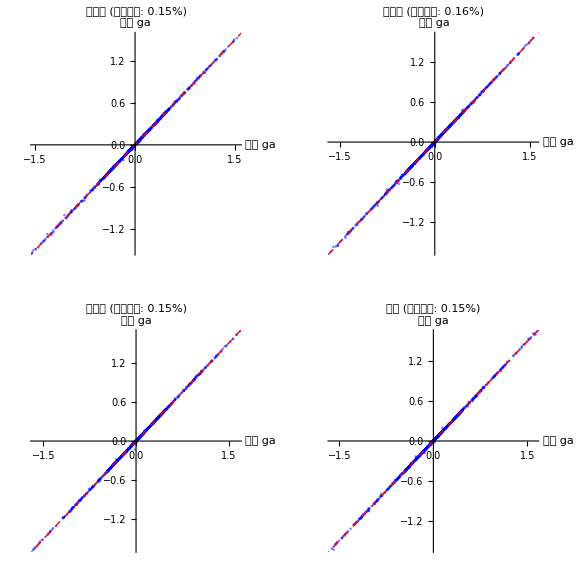

绘制误差分布：

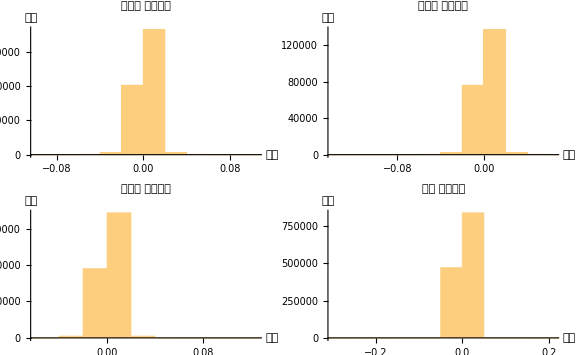

========================================

统计摘要：

========================================

训练集:

样本数: 873655

RMSE: 0.0077

相对误差: 0.15%

最大误差: 0.5781

平均误差: 0.0034

中位误差: 0.0015

验证集:

样本数: 218400

RMSE: 0.0085

相对误差: 0.16%

最大误差: 1.1658

平均误差: 0.0035

中位误差: 0.0015

测试集:

样本数: 218400

RMSE: 0.0078

相对误差: 0.15%

最大误差: 0.7918

平均误差: 0.0035

中位误差: 0.0015

总集:

样本数: 1310455

RMSE: 0.0079

相对误差: 0.15%

最大误差: 1.1658

平均误差: 0.0034

中位误差: 0.0015

✅ 训练完成并保存所有数据到Excel

单独文件:

- training_results.xlsx (训练集，最多10000行)

- validation_results.xlsx (验证集，最多10000行)

- test_results.xlsx (测试集，最多10000行)

- all_results.xlsx (总集，最多10000行)

合并文件:

- combined_results.xlsx (包含4个工作表，每个最多10000行)

```mathematica
(* ==================神经网络训练：二次参数激励Duffing系统==================*)(*输入:[x,v,κ*cos(Ωt),κ*sin(Ωt)]*)(*输出:[ga]=-c*v-α*x-β*x.b3+κ*x.b2*cos(Ωt)*)ClearAll[MyNormalize,EvaluateOnDataset,ExportToExcel];

(*加载数据*)
trainData=Import["trainData_quadratic_parametric.mx"];
valData=Import["valData_quadratic_parametric.mx"];
testData=Import["testData_quadratic_parametric.mx"];

Print["数据加载完成："];
Print["  训练集: ",Length[trainData]," 样本"];
Print["  验证集: ",Length[valData]," 样本"];
Print["  测试集: ",Length[testData]," 样本"];
Print["  总计: ",Length[trainData]+Length[valData]+Length[testData]," 样本"];

(*归一化函数*)
MyNormalize[x_,m_,s_]:=(x-m)/s;

(*提取输入/目标*)
allInputs=trainData[[All,1]];
allTargets=trainData[[All,2]];
inDim=Length[allInputs[[1]]];
outDim=Length[allTargets[[1]]];

Print["输入维度: ",inDim,", 输出维度: ",outDim];

(*统计与标准化*)
inputMean=Mean[allInputs];
inputStd=StandardDeviation[allInputs]+10^-10;
targetMean=Mean[allTargets];
targetStd=StandardDeviation[allTargets]+10^-10;

trainDataNorm=Table[MyNormalize[trainData[[i,1]],inputMean,inputStd]->MyNormalize[trainData[[i,2]],targetMean,targetStd],{i,Length[trainData]}];

valDataNorm=Table[MyNormalize[valData[[i,1]],inputMean,inputStd]->MyNormalize[valData[[i,2]],targetMean,targetStd],{i,Length[valData]}];

testDataNorm=Table[MyNormalize[testData[[i,1]],inputMean,inputStd]->MyNormalize[testData[[i,2]],targetMean,targetStd],{i,Length[testData]}];

(*网络架构*)
net=NetChain[{LinearLayer[64],Tanh,LinearLayer[32],Tanh,LinearLayer[outDim]},"Input"->inDim,"Output"->outDim];

(*通用评估函数-可用于任意数据集*)
EvaluateOnDataset[nn_,dataset_,datasetName_String]:=Module[{inputsNorm,predNorm,pred,true,rmseVec,stdTrueVec,relErrVec,score},inputsNorm=Map[MyNormalize[#,inputMean,inputStd]&,dataset[[All,1]]];
predNorm=nn[inputsNorm];
pred=Map[#*targetStd+targetMean&,predNorm];
true=dataset[[All,2]];
rmseVec=Sqrt@Mean[(pred-true)^2];
stdTrueVec=StandardDeviation/@Transpose[true];
relErrVec=100*rmseVec/stdTrueVec;
score=Mean[rmseVec];
Print["\n",datasetName,"评估："];
Print["  RMSE = ",NumberForm[rmseVec,{6,4}]];
Print["  Rel% = ",NumberForm[relErrVec,{5,2}]];
Print["  Score = ",NumberForm[score,{6,4}]];
<|"rmse"->rmseVec,"rel%"->relErrVec,"score"->score,"pred"->pred,"true"->true,"datasetName"->datasetName|>];

(*分阶段训练*)
stages={<|"rounds"->200,"lr"->0.0005|>,<|"rounds"->3000,"lr"->0.0001|>,<|"rounds"->200,"lr"->0.00005|>,<|"rounds"->200,"lr"->0.00001|>};

Print["\n开始多阶段训练..."];

bestNet=net;
bestStats=<|"score"->Infinity|>;
currNet=net;

Do[Print["\n========== Stage ",si," : rounds=",stages[[si,"rounds"]],", lr=",stages[[si,"lr"]]," =========="];
tr=NetTrain[currNet,trainDataNorm,All,ValidationSet->valDataNorm,MaxTrainingRounds->stages[[si,"rounds"]],BatchSize->1024,LearningRate->stages[[si,"lr"]],Method->{"ADAM"},TargetDevice->"CPU",TrainingProgressReporting->"Panel"];
currNet=tr["TrainedNet"];
stats=EvaluateOnDataset[currNet,valData,"验证集"];
If[stats["score"]<bestStats["score"],bestNet=currNet;
bestStats=stats;
Export["checkpoint_best_stage"<>ToString[si]<>".wlnet",bestNet,"WLNet"];
Print["✅ 更新最佳模型已保存"];];,{si,Length[stages]}];

trainedNet=bestNet;

(*保存模型与归一化参数*)
normParams=<|"inputMean"->inputMean,"inputStd"->inputStd,"targetMean"->targetMean,"targetStd"->targetStd,"targetMeanGa"->targetMean[[1]],"targetStdGa"->targetStd[[1]]|>;

Export["normParams_final.mx",normParams,"MX"];
Export["trainedNet_final.wlnet",trainedNet,"WLNet"];

Print["\n✅ 模型已保存"];

(*评估所有数据集*)
Print["\n========================================"];
Print["最终评估："];
Print["========================================"];

trainResults=EvaluateOnDataset[trainedNet,trainData,"训练集"];
valResults=EvaluateOnDataset[trainedNet,valData,"验证集"];
testResults=EvaluateOnDataset[trainedNet,testData,"测试集"];

(*合并所有数据集评估总体性能*)
allData=Join[trainData,valData,testData];
allResults=EvaluateOnDataset[trainedNet,allData,"总集(全部数据)"];

(*Excel导出函数-带采样选项*)
ExportToExcel[yTrue_,yPred_,errors_,filename_,sheetName_,maxRows_:10000]:=Module[{headers,dataRows,outputData,sampleIndices,actualTrue,actualPred,actualErrors},(*如果数据量超过限制，随机采样*)If[Length[yTrue]>maxRows,Print["⚠ ",sheetName,"数据量(",Length[yTrue],")超过限制，随机采样",maxRows,"行"];
sampleIndices=RandomSample[Range[Length[yTrue]],maxRows];
actualTrue=yTrue[[sampleIndices]];
actualPred=yPred[[sampleIndices]];
actualErrors=errors[[sampleIndices]],actualTrue=yTrue;
actualPred=yPred;
actualErrors=errors];
(*创建表头*)headers={"真实 ga","预测 ga","误差","绝对误差","相对误差(%)"};
(*创建数据行*)dataRows=Table[{actualTrue[[i]],actualPred[[i]],actualErrors[[i]],Abs[actualErrors[[i]]],If[Abs[actualTrue[[i]]]>10^-10,100*Abs[actualErrors[[i]]]/Abs[actualTrue[[i]]],0]},{i,Length[actualTrue]}];
(*组合表头和数据*)outputData=Join[{headers},dataRows];
(*导出到Excel*)Export[filename,outputData,"XLSX"];
Print["✅ ",sheetName,"数据已导出到: ",filename];
Print["   实际导出行数: ",Length[dataRows]," (不含表头)"];];

(*导出所有数据集-设置每个文件最大行数*)
Print["\n========================================"];
Print["导出Excel文件（限制每个数据集最多10000行）："];
Print["========================================"];

maxRowsPerSheet=10000;

(*训练集*)
trainTrue=trainResults["true"][[All,1]];
trainPred=trainResults["pred"][[All,1]];
trainErrors=trainPred-trainTrue;
ExportToExcel[trainTrue,trainPred,trainErrors,"training_results.xlsx","训练集",maxRowsPerSheet];

(*验证集*)
valTrue=valResults["true"][[All,1]];
valPred=valResults["pred"][[All,1]];
valErrors=valPred-valTrue;
ExportToExcel[valTrue,valPred,valErrors,"validation_results.xlsx","验证集",maxRowsPerSheet];

(*测试集*)
testTrue=testResults["true"][[All,1]];
testPred=testResults["pred"][[All,1]];
testErrors=testPred-testTrue;
ExportToExcel[testTrue,testPred,testErrors,"test_results.xlsx","测试集",maxRowsPerSheet];

(*总集-所有数据*)
allTrue=allResults["true"][[All,1]];
allPred=allResults["pred"][[All,1]];
allErrors=allPred-allTrue;
ExportToExcel[allTrue,allPred,allErrors,"all_results.xlsx","总集",maxRowsPerSheet];

(*合并Excel文件-每个sheet限制行数*)
CreateSampledData[yTrue_,yPred_,errors_,maxRows_]:=Module[{sampleIndices,actualTrue,actualPred,actualErrors},If[Length[yTrue]>maxRows,sampleIndices=RandomSample[Range[Length[yTrue]],maxRows];
actualTrue=yTrue[[sampleIndices]];
actualPred=yPred[[sampleIndices]];
actualErrors=errors[[sampleIndices]],actualTrue=yTrue;
actualPred=yPred;
actualErrors=errors];
Join[{{"真实 ga","预测 ga","误差","绝对误差","相对误差(%)"}},Table[{actualTrue[[i]],actualPred[[i]],actualErrors[[i]],Abs[actualErrors[[i]]],If[Abs[actualTrue[[i]]]>10^-10,100*Abs[actualErrors[[i]]]/Abs[actualTrue[[i]]],0]},{i,Length[actualTrue]}]]];

Export["combined_results.xlsx",{"训练集"->CreateSampledData[trainTrue,trainPred,trainErrors,maxRowsPerSheet],"验证集"->CreateSampledData[valTrue,valPred,valErrors,maxRowsPerSheet],"测试集"->CreateSampledData[testTrue,testPred,testErrors,maxRowsPerSheet],"总集"->CreateSampledData[allTrue,allPred,allErrors,maxRowsPerSheet]},"XLSX"];

Print["✅ 合并Excel文件已导出: combined_results.xlsx"];
Print["   包含4个工作表: 训练集、验证集、测试集、总集"];
Print["   每个工作表最多",maxRowsPerSheet,"行数据"];

(*可视化：四个数据集的回归图*)
CreateRegressionPlot[yTrue_,yPred_,title_,relErr_]:=Module[{ymin,ymax,sampleIndices,ySample,pSample},(*如果数据太多，抽样显示*)If[Length[yTrue]>2000,sampleIndices=RandomSample[Range[Length[yTrue]],2000];
ySample=yTrue[[sampleIndices]];
pSample=yPred[[sampleIndices]],ySample=yTrue;
pSample=yPred];
ymin=Min[yTrue];
ymax=Max[yTrue];
ListPlot[Transpose[{ySample,pSample}],PlotStyle->{Blue,PointSize[0.005],Opacity[0.5]},PlotLabel->Row[{title," (相对误差: ",NumberForm[relErr,{5,2}],"%)"}],AxesLabel->{"真实 ga","预测 ga"},AspectRatio->1,ImageSize->Medium,Epilog->{Red,Dashed,Line[{{ymin,ymin},{ymax,ymax}}]}]];

Print["\n绘制回归图："];
trainPlot=CreateRegressionPlot[trainTrue,trainPred,"训练集",trainResults["rel%"][[1]]];
valPlot=CreateRegressionPlot[valTrue,valPred,"验证集",valResults["rel%"][[1]]];
testPlot=CreateRegressionPlot[testTrue,testPred,"测试集",testResults["rel%"][[1]]];
allPlot=CreateRegressionPlot[allTrue,allPred,"总集",allResults["rel%"][[1]]];

GraphicsGrid[{{trainPlot,valPlot},{testPlot,allPlot}},ImageSize->Large]

(*误差分布对比*)
CreateErrorHist[errors_,title_]:=Histogram[errors,50,PlotLabel->title<>" 误差分布",AxesLabel->{"误差","频数"},ImageSize->Medium];

Print["\n绘制误差分布："];
trainErrorHist=CreateErrorHist[trainErrors,"训练集"];
valErrorHist=CreateErrorHist[valErrors,"验证集"];
testErrorHist=CreateErrorHist[testErrors,"测试集"];
allErrorHist=CreateErrorHist[allErrors,"总集"];

GraphicsGrid[{{trainErrorHist,valErrorHist},{testErrorHist,allErrorHist}},ImageSize->Large]

(*统计摘要*)
Print["\n========================================"];
Print["统计摘要："];
Print["========================================"];

PrintStats[results_,name_]:=Module[{errors,maxErr,meanErr,medianErr},errors=Abs[results["pred"][[All,1]]-results["true"][[All,1]]];
maxErr=Max[errors];
meanErr=Mean[errors];
medianErr=Median[errors];
Print[name,":"];
Print["  样本数: ",Length[errors]];
Print["  RMSE: ",NumberForm[results["rmse"][[1]],{6,4}]];
Print["  相对误差: ",NumberForm[results["rel%"][[1]],{5,2}],"%"];
Print["  最大误差: ",NumberForm[maxErr,{6,4}]];
Print["  平均误差: ",NumberForm[meanErr,{6,4}]];
Print["  中位误差: ",NumberForm[medianErr,{6,4}]];];

PrintStats[trainResults,"训练集"];
PrintStats[valResults,"验证集"];
PrintStats[testResults,"测试集"];
PrintStats[allResults,"总集"];

Print["\n✅ 训练完成并保存所有数据到Excel"];
Print["   单独文件:"];
Print["   - training_results.xlsx (训练集，最多",maxRowsPerSheet,"行)"];
Print["   - validation_results.xlsx (验证集，最多",maxRowsPerSheet,"行)"];
Print["   - test_results.xlsx (测试集，最多",maxRowsPerSheet,"行)"];
Print["   - all_results.xlsx (总集，最多",maxRowsPerSheet,"行)"];
Print["   合并文件:"];
Print["   - combined_results.xlsx (包含4个工作表，每个最多",maxRowsPerSheet,"行)"];
```

✅ 模型加载完成

━━━━━━━━━━━━━━━━━━━━━━━━━━━

仿真配置：

二次参数激励: κ=0.35, f_param=1/(2 π) Hz

初值: x₀=1., v₀=0.

时长: 300 s

━━━━━━━━━━━━━━━━━━━━━━━━━━━

━━ RMSE ━━

x(t): 0.0018

v(t): 0.0018

━━ 庞加莱截面 ━━

周期: T=2 π s (f=1/(2 π) Hz)

截面点数: 32

📊 正在导出数据到 Excel...

抽样: 60001 → 4616 点

✅ 数据已导出: case1_quadratic_parametric.xlsx

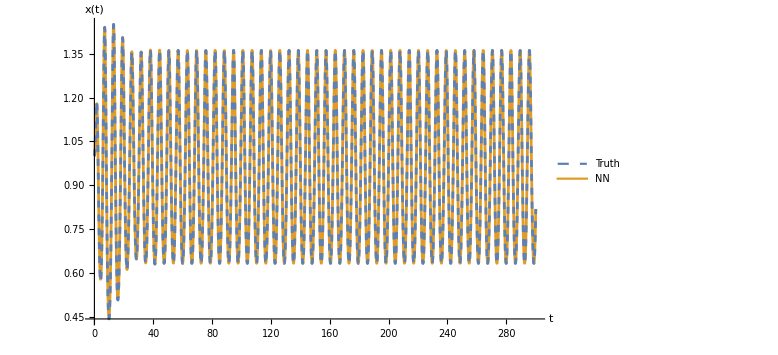

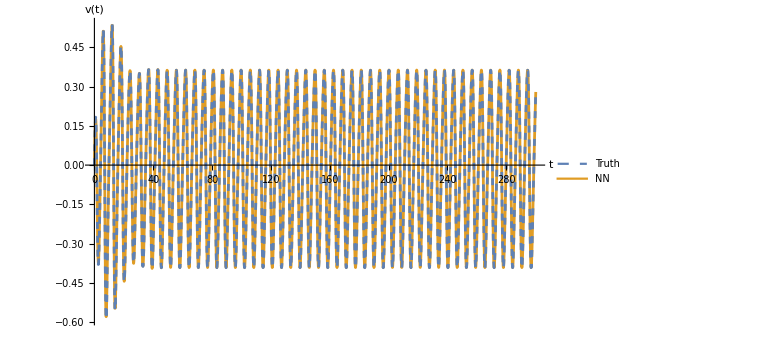

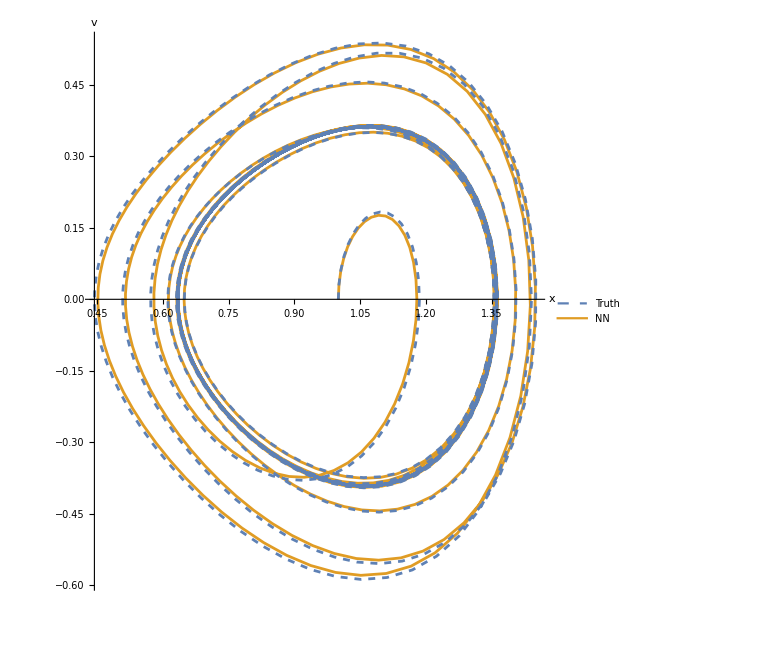

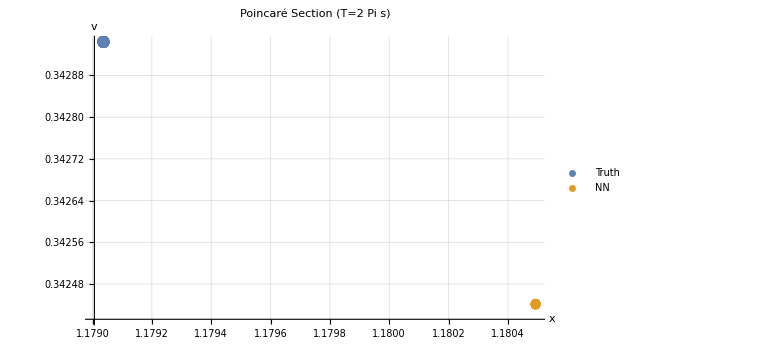

```mathematica
(* =======================1) 载入模型与归一化参数=======================*)If[!ValueQ[trainedNet],trainedNet=Import["trainedNet_final.wlnet"]];
If[!ValueQ[normParams],normParams=Import["normParams_final.mx"]];

inputMean=Lookup[normParams,"inputMean"];
inputStd=Lookup[normParams,"inputStd"];
targetMean=Lookup[normParams,"targetMean",Lookup[normParams,"targetMeanGa",0.]];
targetStd=Lookup[normParams,"targetStd",Lookup[normParams,"targetStdGa",1.]];
scalar[x_]:=First@Flatten@{x};

Print["✅ 模型加载完成"];

(* =======================2) NN 内部加速度（二次参数激励）=======================*)
ClearAll[nnInternalAccel];
(*输入:x,v,κ,Ω,t->输出:ga=-c*v-α*x-β*x.b3+κ*x.b2*cos(Ω*t)*)
nnInternalAccel[x_?NumericQ,v_?NumericQ,κ_?NumericQ,Ω_?NumericQ,t_?NumericQ]:=Module[{kc,ks,z,out},kc=κ*Cos[Ω*t];
ks=κ*Sin[Ω*t];
z=({x,v,kc,ks}-inputMean)/inputStd;
out=trainedNet[z];
scalar[out]*scalar[targetStd]+scalar[targetMean]];

(* =======================3) "真值"方程=======================*)
α=-1.;
β=1.;
c=0.3;

(*二次参数激励方程：ẍ+cẋ+αx+βx.b3=κ x.b2 cos(Ωt)*)
truthAccel[x_,v_,κ_,Ω_,t_]:=-c*v-α*x-β*x^3+κ*x^2*Cos[Ω*t];

(* =======================4) 求解器：NN 系统& 真值系统=======================*)
ClearAll[SolveNN,SolveTruth];

(*NN求解器*)
SolveNN[freqParam_?NumericQ,κ_?NumericQ,x0_?NumericQ,tEnd_?NumericQ,v0_:0.]:=Module[{ΩParam=2*Pi*freqParam},Check[First@NDSolve[{x''[t]==nnInternalAccel[x[t],x'[t],κ,ΩParam,t],x[0]==x0,x'[0]==v0},{x,x'},{t,0,tEnd}],$Failed]];

(*真值求解器*)
SolveTruth[freqParam_?NumericQ,κ_?NumericQ,x0_?NumericQ,tEnd_?NumericQ,v0_:0.]:=Module[{ΩParam=2*Pi*freqParam},Check[First@NDSolve[{x''[t]==truthAccel[x[t],x'[t],κ,ΩParam,t],x[0]==x0,x'[0]==v0},{x,x'},{t,0,tEnd}],$Failed]];

(* =======================5) 对比函数=======================*)
ClearAll[CompareNNvsTruth];
Options[CompareNNvsTruth]={"Dt"->Automatic,"Labels"->{"Truth","NN"},"ExportExcel"->True,"ExcelFilename"->"comparison_quadratic_parametric.xlsx","ExcelMaxPoints"->5000,"PoincareTransient"->100,"PoincareFreq"->Automatic};

CompareNNvsTruth[freqParam_?NumericQ,κ_?NumericQ,x0_?NumericQ,tEnd_?NumericQ,v0_:0.,OptionsPattern[]]:=Module[{ΩParam=2*Pi*freqParam,dt,lbls,solT,solN,xT,vT,xN,vN,tgrid,xTvals,xNvals,vTvals,vNvals,rmseX,rmseV,colorTruth,colorNN,styTruth,styNN,legend,xLine,vLine,phaseLine,exportExcel,excelFile,maxPts,exportStep,tgridExport,dataTable,summaryTable,poincareTransient,period,poincFreq,tPoincare,xTpoincare,vTpoincare,xNpoincare,vNpoincare,poincarePlot},(*样式设置*)colorTruth=RGBColor[0.368,0.507,0.710];
colorNN=RGBColor[0.880,0.611,0.142];
styTruth=Directive[colorTruth,Dashed,Thick];
styNN=Directive[colorNN,Thick];
lbls=OptionValue["Labels"];
legend=Placed[LineLegend[{styTruth,styNN},lbls],After];
exportExcel=OptionValue["ExportExcel"];
excelFile=OptionValue["ExcelFilename"];
maxPts=OptionValue["ExcelMaxPoints"];
poincareTransient=OptionValue["PoincareTransient"];
dt=OptionValue["Dt"]/. Automatic->(1./(200.*Max[1.,freqParam]));
(*确定庞加莱截面采样频率*)poincFreq=OptionValue["PoincareFreq"]/. Automatic->freqParam;
period=1/poincFreq;
Print["━━━━━━━━━━━━━━━━━━━━━━━━━━━"];
Print["仿真配置："];
Print["  二次参数激励: κ=",κ,", f_param=",NumberForm[freqParam,{4,3}]," Hz"];
Print["  初值: x₀=",x0,", v₀=",v0];
Print["  时长: ",tEnd," s"];
Print["━━━━━━━━━━━━━━━━━━━━━━━━━━━"];
(*求解系统*)solT=SolveTruth[freqParam,κ,x0,tEnd,v0];
If[solT===$Failed,Print["❌ 真值系统 NDSolve 未收敛。"];
Return[$Failed]];
solN=SolveNN[freqParam,κ,x0,tEnd,v0];
If[solN===$Failed,Print["❌ 神经网络系统 NDSolve 未收敛。"];
Return[$Failed]];
xT=x/. solT;vT=x'/. solT;
xN=x/. solN;vN=x'/. solN;
(*生成时间网格和数据*)tgrid=N@Range[0,tEnd,dt];
xTvals=xT/@tgrid;xNvals=xN/@tgrid;
vTvals=vT/@tgrid;vNvals=vN/@tgrid;
(*计算误差指标*)rmseX=Sqrt@Mean[(xNvals-xTvals)^2];
rmseV=Sqrt@Mean[(vNvals-vTvals)^2];
Print["━━ RMSE ━━"];
Print["  x(t): ",NumberForm[rmseX,{6,4}]];
Print["  v(t): ",NumberForm[rmseV,{6,4}]];
(*计算庞加莱截面*)tPoincare=Select[Range[poincareTransient,tEnd,period],#<=tEnd&];
If[Length[tPoincare]>0,xTpoincare=xT/@tPoincare;
vTpoincare=vT/@tPoincare;
xNpoincare=xN/@tPoincare;
vNpoincare=vN/@tPoincare;
Print["━━ 庞加莱截面 ━━"];
Print["  周期: T=",NumberForm[period,{6,4}]," s (f=",NumberForm[poincFreq,{6,4}]," Hz)"];
Print["  截面点数: ",Length[tPoincare]];,Print["⚠️ 警告: 模拟时间太短，无法生成庞加莱截面"];
xTpoincare={};vTpoincare={};
xNpoincare={};vNpoincare={};];
(*Excel导出*)If[exportExcel,Print["📊 正在导出数据到 Excel..."];
If[Length[tgrid]>maxPts,exportStep=Ceiling[Length[tgrid]/maxPts];
tgridExport=tgrid[[1;;-1;;exportStep]];
Print["   抽样: ",Length[tgrid]," → ",Length[tgridExport]," 点"];,tgridExport=tgrid;
exportStep=1;];
dataTable=Join[{{"Time (t)","x_Truth","x_NN","v_Truth","v_NN","Error_x","Error_v"}},Transpose[{tgridExport,(xT/@tgridExport),(xN/@tgridExport),(vT/@tgridExport),(vN/@tgridExport),(xN/@tgridExport)-(xT/@tgridExport),(vN/@tgridExport)-(vT/@tgridExport)}]];
If[Length[tPoincare]>0,poincareTable=Join[{{"Time (t)","x_Truth","v_Truth","x_NN","v_NN"}},Transpose[{tPoincare,xTpoincare,vTpoincare,xNpoincare,vNpoincare}]];,poincareTable={{"Time (t)","x_Truth","v_Truth","x_NN","v_NN"},{"N/A","N/A","N/A","N/A","N/A"}};];
summaryTable={{"Parameter","Value"},{"Quadratic Parametric Excitation",""},{"  Amplitude (κ)",κ},{"  Frequency (Hz)",freqParam},{"  Omega (rad/s)",ΩParam},{"Initial Conditions",""},{"  Position (x₀)",x0},{"  Velocity (v₀)",v0},{"Simulation",""},{"  Total Time (s)",tEnd},{"  Time Step (dt)",dt},{"  Total Points",Length[tgrid]},{"  Exported Points",Length[tgridExport]},{"Poincare Section",""},{"  Sampling Frequency (Hz)",poincFreq},{"  Period (s)",period},{"  Transient Time (s)",poincareTransient},{"  Points",Length[tPoincare]},{"RMSE Metrics",""},{"  RMSE x(t)",rmseX},{"  RMSE v(t)",rmseV},{"System Parameters",""},{"  Alpha (α)",α},{"  Beta (β)",β},{"  Damping (c)",c}};
Export[excelFile,{"Time History"->dataTable,"Poincare Section"->poincareTable,"Summary"->summaryTable},"XLSX"];
Print["✅ 数据已导出: ",excelFile];];
(*生成图形*)xLine=Plot[{xN[t],xT[t]},{t,0,tEnd},PlotStyle->{styNN,styTruth},PlotLegends->legend,AxesLabel->{"t","x(t)"},PlotRange->All,ImageSize->Large];
vLine=Plot[{vN[t],vT[t]},{t,0,tEnd},PlotStyle->{styNN,styTruth},PlotLegends->legend,AxesLabel->{"t","v(t)"},PlotRange->All,ImageSize->Large];
phaseLine=ParametricPlot[{{xN[t],vN[t]},{xT[t],vT[t]}},{t,0,tEnd},PlotStyle->{styNN,styTruth},PlotLegends->legend,AxesLabel->{"x","v"},PlotRange->All,ImageSize->Large];
If[Length[tPoincare]>0,poincarePlot=ListPlot[{Transpose[{xTpoincare,vTpoincare}],Transpose[{xNpoincare,vNpoincare}]},PlotStyle->{Directive[colorTruth,PointSize[0.015]],Directive[colorNN,PointSize[0.012]]},PlotLegends->Placed[PointLegend[{colorTruth,colorNN},lbls],After],AxesLabel->{"x","v"},PlotLabel->"Poincaré Section (T="<>ToString[NumberForm[period,3]]<>" s)",PlotRange->All,ImageSize->Large,GridLines->Automatic];,poincarePlot=Graphics[Text[Style["庞加莱截面：模拟时间不足",16,Red],{0,0}],ImageSize->Large];];
Print@xLine;
Print@vLine;
Print@phaseLine;
Print@poincarePlot;
<|"TimeGrid"->tgrid,"xTruth"->xTvals,"xNN"->xNvals,"vTruth"->vTvals,"vNN"->vNvals,"PoincareTimes"->tPoincare,"PoincareXTruth"->xTpoincare,"PoincareVTruth"->vTpoincare,"PoincareXNN"->xNpoincare,"PoincareVNN"->vNpoincare,"RMSE_x"->rmseX,"RMSE_v"->rmseV,"Period"->period,"ExcelFile"->If[exportExcel,excelFile,None]|>];

(* =======================6) 使用示例=======================*)


result1=CompareNNvsTruth[1/(2*Pi),(*freqParam:参数激励频率*)0.35,(*κ:参数激励幅值*)1.0,(*x0:初始位置*)300,(*tEnd:仿真时长*)0.,(*v0:初始速度*)"ExcelFilename"->"case1_quadratic_parametric.xlsx"];
```

扫频配置：

参数激励: κ=0, f_param=0.016 Hz (固定)

外激励扫频: f_force ∈ [0.0795775, 0.238732] Hz

外激励幅值: F=0.2

前扫进度：

10/201

20/201

30/201

40/201

50/201

60/201

70/201

80/201

90/201

100/201

110/201

120/201

130/201

140/201

150/201

160/201

170/201

180/201

190/201

200/201

201/201

后扫进度：

10/201

20/201

30/201

40/201

50/201

60/201

70/201

80/201

90/201

100/201

110/201

120/201

130/201

140/201

150/201

160/201

170/201

180/201

190/201

200/201

201/201

绘制幅频响应曲线：

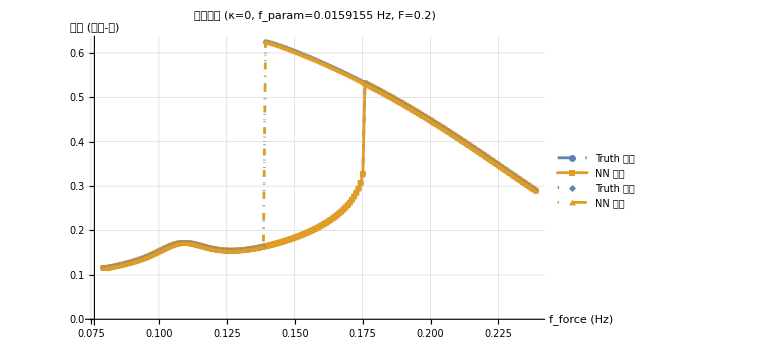

绘制RMSE误差曲线：

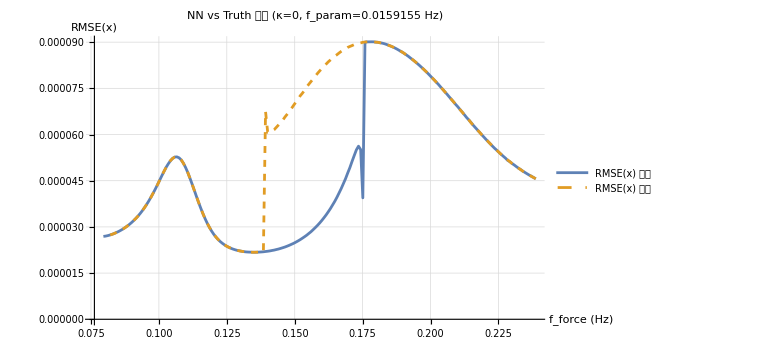

✅ 数据已保存到: frf_parametric_force_sweep.mx

```mathematica
(* ======================NN& 真值：扫描二次参数激励频率======================*)ClearAll[FRFSweepQuadraticParam,PlotFRFNNTruth,PlotRMSEFRF];

FRFSweepQuadraticParam[freqMin_:0.5,(*参数激励频率范围*)freqMax_:1.5,dFreq_:0.01,(*频率步长*)κ_:0.2,(*参数激励幅值*)cyclesSettle_:60,(*稳定周期数*)cyclesMeasure_:20,(*测量周期数*)dt_:Automatic,ic_:Automatic,carryFrom_:"truth"   (*续接策略:"truth","nn","self"*)]:=Module[{stables,ic0,doOne,updateIC,forwardGrid,backwardGrid,forward={},backward={},initTruth,initNN},(*起始平衡（右井）*)stables=FindStableEq[α,β,0];
If[Length[stables]<2,Print["❌ 未找到两个稳定平衡"];
Return[$Failed]];
ic0=If[ic===Automatic,{stables[[2]],0.0},ic];
Print["扫频配置："];
Print["  二次参数激励: κ=",κ];
Print["  扫频范围: f ∈ [",freqMin,", ",freqMax,"] Hz"];
Print["  频率步长: Δf=",dFreq," Hz"];
Print["  续接策略: ",carryFrom];
(*单个频点：两套系统同步积分与度量*)doOne[freq_?NumericQ,{x0T_,v0T_},{x0N_,v0N_}]:=Module[{T,tS,tM,tEnd,dtsamp,solT,solN,xT,vT,xN,vN,ts,xTs,vTs,xNs,vNs,xminT,xmaxT,xminN,xmaxN,ampT,ampN,meanT,meanN,rmx,rmv,lastT,lastN,okT=True,okN=True},T=1/freq;(*基于参数激励周期*)tS=cyclesSettle*T;
tM=cyclesMeasure*T;
tEnd=tS+tM;
dtsamp=Replace[dt,Automatic->(1./(200.*freq))];
(*真值求解*)solT=SolveTruth[freq,κ,x0T,tEnd,v0T];
If[solT===$Failed,okT=False,xT=x/. solT;
vT=x'/. solT];
(*NN求解*)solN=SolveNN[freq,κ,x0N,tEnd,v0N];
If[solN===$Failed,okN=False,xN=x/. solN;
vN=x'/. solN];
(*采样与度量*)ts=Range[tS,tEnd,dtsamp];
If[okT,xTs=xT/@ts;vTs=vT/@ts;
xminT=Min[xTs];xmaxT=Max[xTs];meanT=Mean[xTs];
ampT=(xmaxT-xminT)/2.;
lastT={xT[tEnd],vT[tEnd]},lastT={x0T,v0T}];
If[okN,xNs=xN/@ts;vNs=vN/@ts;
xminN=Min[xNs];xmaxN=Max[xNs];meanN=Mean[xNs];
ampN=(xmaxN-xminN)/2.;
lastN={xN[tEnd],vN[tEnd]},lastN={x0N,v0N}];
If[okT&&okN,rmx=Sqrt@Mean[(xNs-xTs)^2];
rmv=Sqrt@Mean[(vNs-vTs)^2],rmx=Missing[];
rmv=Missing[]];
<|"freq"->freq,"Truth"-><|"Amp"->ampT,"Mean"->meanT,"xmax"->xmaxT,"xmin"->xminT,"ok"->okT|>,"NN"-><|"Amp"->ampN,"Mean"->meanN,"xmax"->xmaxN,"xmin"->xminN,"ok"->okN|>,"RMSE"-><|"x"->rmx,"v"->rmv|>,"endTruth"->lastT,"endNN"->lastN|>];
(*续接策略*)updateIC[res_Association]:=Module[{xvT=res["endTruth"],xvN=res["endNN"]},Switch[carryFrom,"truth",{xvT,xvT},"nn",{xvN,xvN},"self"|"independent",{xvT,xvN},_,{xvT,xvT}]];
(*前扫*)forwardGrid=Range[freqMin,freqMax,dFreq];
{initTruth,initNN}={ic0,ic0};
Print["前扫进度："];
Do[If[Mod[i,10]==0||i==Length[forwardGrid],Print["  ",i,"/",Length[forwardGrid]]];
With[{r=doOne[forwardGrid[[i]],initTruth,initNN]},AppendTo[forward,KeyDrop[r,{"endTruth","endNN"}]];
{initTruth,initNN}=updateIC[r]],{i,Length[forwardGrid]}];
(*后扫：先在 freqMax 热身*){initTruth,initNN}=updateIC[doOne[freqMax,ic0,ic0]];
backwardGrid=Range[freqMax,freqMin,-dFreq];
Print["后扫进度："];
Do[If[Mod[i,10]==0||i==Length[backwardGrid],Print["  ",i,"/",Length[backwardGrid]]];
With[{r=doOne[backwardGrid[[i]],initTruth,initNN]},AppendTo[backward,KeyDrop[r,{"endTruth","endNN"}]];
{initTruth,initNN}=updateIC[r]],{i,Length[backwardGrid]}];
<|"forward"->forward,"backward"->backward,"meta"-><|"kappa"->κ,"cyclesSettle"->cyclesSettle,"cyclesMeasure"->cyclesMeasure,"dt"->dt,"carryFrom"->carryFrom|>|>];

(* ============================绘图：幅频比较============================*)
PlotFRFNNTruth[frf_Association,key_:"Amp"]:=Module[{extract,fT,fN,bT,bN,meta},extract[dir_,model_]:=Module[{lst=frf[dir]},Cases[lst,a_Association/;KeyExistsQ[a,model]&&NumericQ[a[model][key]]:>{a["freq"],a[model][key]}]];
fT=extract["forward","Truth"];
fN=extract["forward","NN"];
bT=extract["backward","Truth"];
bN=extract["backward","NN"];
meta=frf["meta"];
ListLinePlot[{fT,fN,bT,bN},PlotLegends->{"Truth 前扫","NN 前扫","Truth 后扫","NN 后扫"},PlotStyle->{Directive[RGBColor[0.368,0.507,0.710],Dashed,Thick],Directive[RGBColor[0.880,0.611,0.142],Thick],Directive[RGBColor[0.368,0.507,0.710],Dotted,Thick],Directive[RGBColor[0.880,0.611,0.142],DotDashed,Thick]},PlotMarkers->{Automatic,6},AxesLabel->{"f (Hz)",Switch[key,"Amp","幅值 (半峰-峰)","Mean","均值",_,key]},PlotLabel->StringTemplate["频率响应 (二次参数激励, κ=``)"][meta["kappa"]],GridLines->Automatic,ImageSize->Large,PlotRange->All]];

(* ============================绘图：RMSE 随频率============================*)
PlotRMSEFRF[frf_Association,comp_:"x"]:=Module[{ext,meta},ext[dir_]:=Module[{lst=frf[dir]},Cases[lst,a_Association/;!MissingQ[a["RMSE"][comp]]&&NumericQ[a["RMSE"][comp]]:>{a["freq"],a["RMSE"][comp]}]];
meta=frf["meta"];
ListLinePlot[{ext["forward"],ext["backward"]},PlotLegends->{"RMSE("<>comp<>") 前扫","RMSE("<>comp<>") 后扫"},PlotStyle->{Directive[Thick],Directive[Dashed,Thick]},AxesLabel->{"f (Hz)","RMSE("<>comp<>")"},PlotLabel->StringTemplate["NN vs Truth 误差 (二次参数激励, κ=``)"][meta["kappa"]],GridLines->Automatic,ImageSize->Large,PlotRange->All]];

(* ============================使用示例============================*)

(*测试1:扫描二次参数激励频率*)
frf1=FRFSweepQuadraticParam[0.5/(2*Pi),(*最小频率*)1.5/(2*Pi),(*最大频率*)0.005/(2*Pi),(*频率步长*)0.2,(*激励幅值 κ*)60,(*稳定周期数*)20,(*测量周期数*)Automatic,(*时间步长*)Automatic,(*初始条件*)"truth"             (*续接策略*)];

Print["\n绘制幅频响应曲线："];
PlotFRFNNTruth[frf1,"Amp"]

Print["\n绘制RMSE误差曲线："];
PlotRMSEFRF[frf1,"x"]

(* ============================导出数据============================*)
Export["frf_quadratic_parametric.mx",frf1,"MX"];
Print["✅ 数据已保存到: frf_quadratic_parametric.mx"];

(* ============================导出到Excel============================*)

(*提取前扫数据*)
forwardData=Module[{lst=frf1["forward"]},Table[With[{a=lst[[i]]},{a["freq"],a["Truth"]["Amp"],a["Truth"]["Mean"],a["Truth"]["xmax"],a["Truth"]["xmin"],a["NN"]["Amp"],a["NN"]["Mean"],a["NN"]["xmax"],a["NN"]["xmin"],If[MissingQ[a["RMSE"]["x"]],"",a["RMSE"]["x"]],If[MissingQ[a["RMSE"]["v"]],"",a["RMSE"]["v"]]}],{i,Length[lst]}]];

(*提取后扫数据*)
backwardData=Module[{lst=frf1["backward"]},Table[With[{a=lst[[i]]},{a["freq"],a["Truth"]["Amp"],a["Truth"]["Mean"],a["Truth"]["xmax"],a["Truth"]["xmin"],a["NN"]["Amp"],a["NN"]["Mean"],a["NN"]["xmax"],a["NN"]["xmin"],If[MissingQ[a["RMSE"]["x"]],"",a["RMSE"]["x"]],If[MissingQ[a["RMSE"]["v"]],"",a["RMSE"]["v"]]}],{i,Length[lst]}]];

(*创建表头*)
headers={"f (Hz)","Truth_Amp","Truth_Mean","Truth_xmax","Truth_xmin","NN_Amp","NN_Mean","NN_xmax","NN_xmin","RMSE_x","RMSE_v"};

(*添加元数据*)
meta=frf1["meta"];
metaInfo={{"二次参数激励幅值 κ",meta["kappa"]},{"稳定周期数",meta["cyclesSettle"]},{"测量周期数",meta["cyclesMeasure"]},{"续接策略",meta["carryFrom"]},{"",""}};

(*组合前扫数据*)
forwardSheet=Join[{{"前扫数据 (Forward Sweep)"}},metaInfo,{headers},forwardData];

(*组合后扫数据*)
backwardSheet=Join[{{"后扫数据 (Backward Sweep)"}},metaInfo,{headers},backwardData];

(*导出到Excel*)
Export["FRF_Results_Quadratic.xlsx",{"Forward"->forwardSheet,"Backward"->backwardSheet},"XLSX"];

Print["✅ Excel文件已导出: FRF_Results_Quadratic.xlsx"];

(* ============================额外测试案例============================*)

(*测试2:较大激励幅值*)
frf2=FRFSweepQuadraticParam[0.3,(*最小频率*)1.0,(*最大频率*)0.01,(*频率步长*)0.5,(*激励幅值 κ*)40,(*稳定周期数*)15,(*测量周期数*)Automatic,Automatic,"truth"];

Print["\n绘制幅频响应曲线（大幅值）："];
PlotFRFNNTruth[frf2,"Amp"]

(*测试3:自续接策略*)
frf3=FRFSweepQuadraticParam[0.4,(*最小频率*)1.2,(*最大频率*)0.008,(*频率步长*)0.3,(*激励幅值 κ*)50,(*稳定周期数*)20,(*测量周期数*)Automatic,Automatic,"self"              (*各自续接*)];

Print["\n✅ 所有扫频测试完成！"];
```